# Initialize

```mathematica
ReadQfile[fpath_]:=
Module[{s,table},
s=OpenRead[fpath];
table=ReadList[s,Number];
Close[s];
Return[table]
];
```

```mathematica
(* next step: Import data from station*)
ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]:=
Module[{s,table,L},
s=OpenRead[fpath];
table=ReadList[s,String];
Close[s];
L=Length[table];

table=Table[0,{L-headerrows}];
s=OpenRead[fpath];
Skip[s,String,headerrows];

Do[
Skip[s,Word,columnofinterest-1];
table[[i]]=Read[s,format];
Skip[s,Word,ncolumns-columnofinterest];
,{i,L-headerrows}];
Close[s];

Return[table]
];
```

```mathematica
makemodelscatter[modelresults_,modelstn_,modelts_,timestart_,scalar_,offset_]:=
Module[{qtable,timetable,modelscatter},
qtable=Table[(modelresults[[modelstn]][[i]]*scalar+offset),{i,1,Length[modelresults[[modelstn]]]}];
timetable=Table[timestart+(i*modelts),{i,1,Length[modelresults[[modelstn]]]}];
modelscatter=Transpose[Table[{timetable,qtable}]];
Return[modelscatter]
];
(*model ts = the models' timestep, in units of the x-axis unit of the graph. E.g. with 10 minute output timestep for a fort.61, to show a graph in days requires "modelts" = 10 min / 60*24 (min/day) = 1/144. 5-minute would be 1/288.*)
```

```mathematica
scattercompare[modelscatter_,obscatter_]:=
Show[ListPlot[modelscatter,Joined->True,PlotRange->Full],ListPlot[obscatter,PlotStyle->Black,PlotMarkers->{Automatic,4}]];
```

# Load Model Results

```mathematica
wselist=Table[0,{12}];
scatterlist=Table[0,{12}];
(*Do[*)
filelist=
{
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8652587_WSE_Timeseries_Spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8652587_WSE_Timeseries_Hurricane.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8652587_WSE_Timeseries_Spindown.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084000_WSE_Timeseries_spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084000_WSE_Timeseries_Hur.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084000_WSE_Timeseries_spindown.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_Hur.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\02084472_WSE_Timeseries_spindown.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8651370_WSE_Timeseries_Spinup.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8651370_WSE_Timeseries_Hurricane.txt",
"C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\results\\8651370_WSE_Timeseries_Spindown.txt"
};

(*replaced; for irene the "spindown" fort.61 reflects the entire combined solution*)
Do[
fpath=filelist[[j]];
wselist[[j]]=ReadQfile[fpath];
(*,{i,1,Length[runlist]}];*)
,{j,1,12}];

(*next step: timestamp each one in 10 minute intervals. date label scheme: days past run start date*)
startlist={0,45,55,0,45,55,0,45,55,0,45,55};
offsetlist={0,0,0,3.54,3.54,3.54,1,1,1,0,0,0};(*datum offset to convert ADCIRC results to common datum with gauge*)

Do[
scatterlist[[i]]=makemodelscatter[wselist,i,(1/288),startlist[[i]],3.28084,offsetlist[[i]]]
,{i,1,12}]
```

# Water Surface Elevations - 02084000

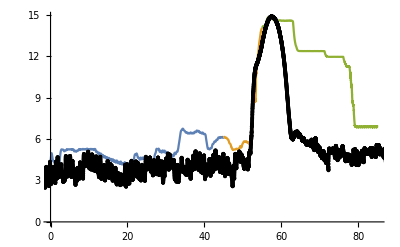

```mathematica
(*02083500*)
(*ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]*)
Quiet[
fpath="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\observed\\02084000_filled.txt";
headerrows=1;
ncols=5;
datecol=1;
timecol=2;
stagecol=4;
stageseries=ReadUSGSQfile[fpath,headerrows,ncols,stagecol,Number];
dateseries=ReadUSGSQfile[fpath,headerrows,ncols,datecol,Word];
timeseries=ReadUSGSQfile[fpath,headerrows,ncols,timecol,Word];
abstimeseries=Table[AbsoluteTime[StringJoin[dateseries[[i]]," ",timeseries[[i]]]],{i,1,Length[timeseries]}];
stormstart=AbsoluteTime["2011,07,06"];
abstimeseriesdays=(abstimeseries-stormstart)/86400;
Obscatter02084000=Transpose[Table[{abstimeseriesdays,stageseries}]];
];

scattercompare[scatterlist[[4;;6]],Obscatter02084000]
```

# Water Surface Elevations - 02084472

```mathematica
(*02084472*)
(*ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]*)
Quiet[
fpath="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\observed stage\\02084472.txt";
headerrows=26;
ncols=7;
datecol=3;
timecol=4;
stagecol=6;
stageseries=ReadUSGSQfile[fpath,headerrows,ncols,stagecol,Number];
dateseries=ReadUSGSQfile[fpath,headerrows,ncols,datecol,Word];
timeseries=ReadUSGSQfile[fpath,headerrows,ncols,timecol,Word];
abstimeseries=Table[AbsoluteTime[StringJoin[dateseries[[i]]," ",timeseries[[i]]]]+4*3600,{i,1,Length[timeseries]}];
stormstart=AbsoluteTime["2011,07,06"];
abstimeseriesdays=(abstimeseries-stormstart)/86400;
Obscatter02084472=Transpose[Table[{abstimeseriesdays,stageseries}]];
];
```

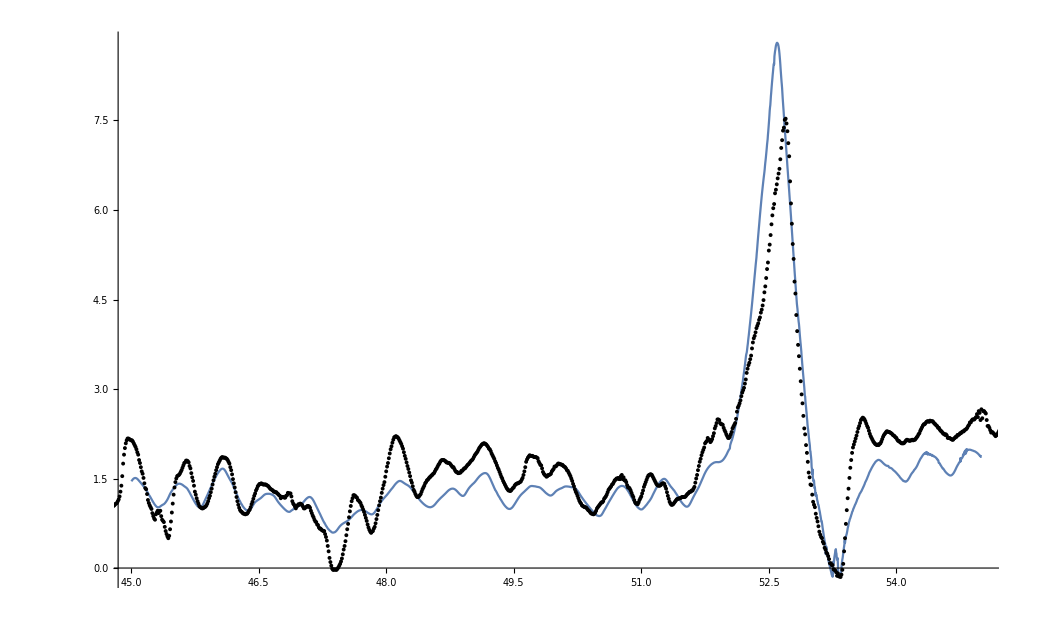

```mathematica
scattercompare[scatterlist[[8]],Obscatter02084472]
```

# Water Surface Elevations - 8652587

```mathematica
(*ReadUSGSQfile[fpath_,headerrows_,ncolumns_,columnofinterest_,format_]*)
Quiet[
fpath="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\observed stage\\8652587.txt";
headerrows=1;
ncols=9;
datecol=1;
timecol=2;
stagecol=3;
stageseries=ReadUSGSQfile[fpath,headerrows,ncols,stagecol,Number];
dateseries=ReadUSGSQfile[fpath,headerrows,ncols,datecol,Word];
timeseries=ReadUSGSQfile[fpath,headerrows,ncols,timecol,Word];
abstimeseries=Table[AbsoluteTime[StringJoin[dateseries[[i]]," ",timeseries[[i]]]],{i,1,Length[timeseries]}];
stormstart=AbsoluteTime["2011,07,06"];
abstimeseriesdays=(abstimeseries-stormstart)/86400;
Obscatter8652587=Transpose[Table[{abstimeseriesdays,stageseries}]];
];
```

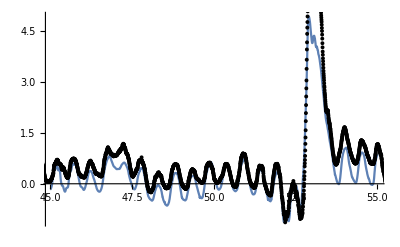

```mathematica
scattercompare[scatterlist[[2]],Obscatter8652587]
```

```mathematica
Transpose[Obscatter8652587][[1]]
```

{0,1/240,1/120,1/80,1/60,1/48,1/40,7/240,1/30,3/80,1/24,11/240,1/20,13/240,7/120,1/16,1/15,17/240,3/40,19/240,1/12,7/80,11/120,23/240,1/10,5/48,13/120,9/80,7/60,29/240,1/8,31/240,2/15,11/80,17/120,7/48,3/20,37/240,19/120,13/80,1/6,41/240,7/40,43/240,11/60,3/16,23/120,20546,20593/240,10297/120,1373/16,5149/60,20597/240,3433/40,20599/240,515/6,6867/80,10301/120,20603/240,1717/20,4121/48,10303/120,6869/80,1288/15,20609/240,687/8,20611/240,5153/60,6871/80,10307/120,4123/48,859/10,20617/240,10309/120,6873/80,1031/12,20621/240,3437/40,20623/240,1289/15,1375/16,10313/120,20627/240,1719/20,20629/240,2063/24,6877/80,2579/30,20633/240,3439/40,4127/48,5159/60,6879/80,10319/120,20639/240}
 |  |  |  |

```mathematica
scatterNS[obscatter_,modelscatter_,timeinc_]:=
Catch[
Module[{L,times1,vals1,times2,vals2,commonstart,commonend,bin,binstart,binstop,obqs,modqs,gaps,obqm,topsumsq,botsumsq,nse},



(*let's say we want to do an N-S calculation on a 15-minute time interval.*)
(*step 1 is to calculate the extent of each scatter*)
times1=Transpose[obscatter][[1]];
vals1=Transpose[obscatter][[2]];
times2=Transpose[modelscatter][[1]];
vals2=Transpose[modelscatter][[2]];
commonstart=Max[Min[times1],Min[times2]];
commonend=Min[Max[times1],Max[times2]];
L=(commonend-commonstart)/timeinc;
L=Ceiling[L];


(*step one is to find out how many 15-minute intervals there are, shared among the two scatters.*)
(*this method assumes the scatters start at about the same time*)

(*bin is a table of the observations or forecasts in each 15-minute interval*)
bin=Table[{{},{}},{L}];

(*for each bin, calculate the time extents*)
Do[
binstart=commonstart+(i-1)*timeinc;
binstop=commonstart+i*timeinc;

(*collect obscatter's entries that fit the bin*)
Do[
If[times1[[j]]<binstop,
If[times1[[j]]≥binstart,
bin[[i,1]]=Flatten[Append[bin[[i,1]],vals1[[j]]]];
];
];
,{j,1,Length[obscatter]}];

(*collect modelscatter's entries that fit the bin*)
Do[
If[times2[[j]]<binstop,
If[times2[[j]]≥binstart,
bin[[i,2]]=Flatten[Append[bin[[i,2]],vals2[[j]]]];
];
];
,{j,1,Length[modelscatter]}];

,{i,1,L}];

(*now that all bins are populated, delete gaps:*)

(*and replace all (extant) bins with the mean of the contents of that bin, separated by *)
Do[
Do[
If[bin[[i,j]]≠{},
bin[[i,j]]=Mean[bin[[i,j]]];
];
,{j,1,2}];
,{i,1,Length[bin]}];
obqs=Transpose[bin][[1]];
modqs=Transpose[bin][[2]];
(*remove gaps - pass 1*)
gaps=Position[obqs,{}];
obqs=Delete[obqs,gaps];
modqs=Delete[modqs,gaps];
(*remove gaps - pass 2*)
gaps=Position[modqs,{}];
obqs=Delete[obqs,gaps];
modqs=Delete[modqs,gaps];
(*calculate NSE*)
-Graphics-
obqs=Flatten[obqs];
modqs=Flatten[modqs];
obqm=Mean[obqs];

topsumsq=Sum[(obqs[[i]]-modqs[[i]])^2,{i,1,Length[obqs[[i]]]}];
botsumsq=Sum[(obqs[[i]]-obqm)^2,{i,1,Length[obqs[[i]]]}];
nse=1-(topsumsq)/(botsumsq);
Throw[nse];
]];
```

# 8651370

```mathematica
fpath="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\observed stage\\8651370.csv";
raw=Import[fpath];
raw=Delete[raw,1];
stageseries=Transpose[raw][[2]];
datetime=Transpose[raw][[1]];
abstimeseries=Table[AbsoluteTime[datetime[[i]]],{i,1,Length[datetime]}];
stormstart=AbsoluteTime["2011,07,06"];
abstimeseriesdays=(abstimeseries-stormstart)/86400;
Obscatter8651370=Transpose[Table[{abstimeseriesdays,stageseries}]];
```

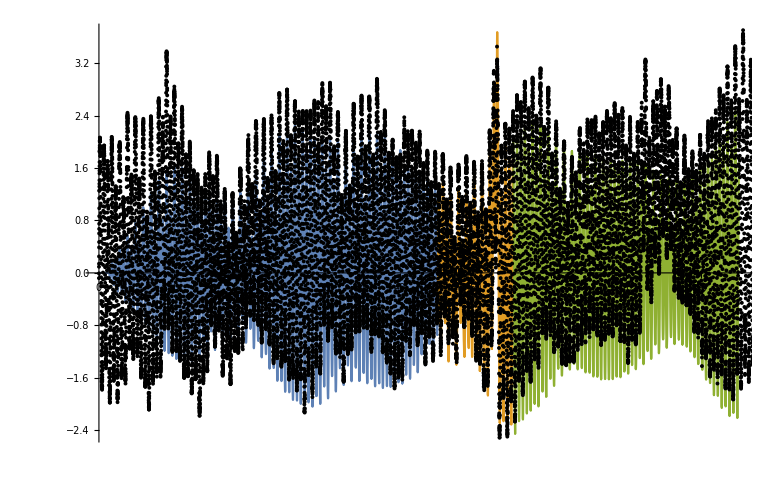

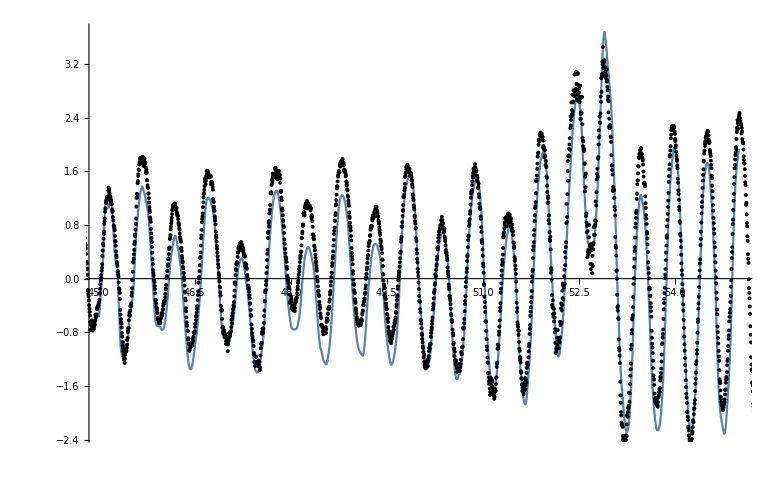

```mathematica
scattercompare[scatterlist[[10;;12]],Obscatter8651370]
scattercompare[scatterlist[[11]],Obscatter8651370]
```

```mathematica
nashsutcliffe
```